```mathematica
Clear["Global`*"]
P[1]={1,-1/3,5/6,1/9,1/9,1/9}; (*(27,1,0)*)
P[2]={1,-1/8,5/6,7/48,-1/36,-1/36};(*(15,2,5/6)*)
P[3]={1,1/12,5/6,13/72,13/72,-1/6}; (*(6,3,5/3)*)
P[4]={1,1/12,5/6,13/72,-1/6,1/144}; (*(8,3,0)*)
P[5]={1,7/24,5/6,31/144,1/24,1/24}; (*(3,4,5/6)*)
P[6]={1,1/2, 5/6,1/4,1/4,1/4}; (*(1,5,0)*)
P[7]={1,-1/28,5/6,9/56,-11/126,37/1008}; (*(8,1,0)*)
P[8]={1,11/42,5/6,53/253,1/84,1/9};(*(1,3,0)*)
P[9]={1,1/7,5/6,4/21,-1/126,23/252}; (*(1,1,0)*)
P[10]={1,19/168,5/6,187/1008,1/84,1/84};(*(3,2,5/6)*)
```

```mathematica
b= ϵ V;(*ϵ=V/Λ*)
m=Table[P[i],{i,1,10}];(*Raccolgo tutti i coefficenti in un'unica matrice*)
x={mf,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3], Subscript[c, 4],Subscript[c, 5]};
x1={1,V,b,b,b,b};
z= x x1;
y={Subscript[M, 1],Subscript[M, 2],Subscript[M, 3],Subscript[M, 4],Subscript[M, 5],0,Subscript[M, 7],Subscript[M, 8],Subscript[M, 9],Subscript[M, 10]}; (*Subscript[M, 6] è messa a 0 essendo il quintupletto*)
sol=Solve[m.z==y ,{mf,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[M, 2],Subscript[M, 4],Subscript[M, 5],Subscript[M, 7],Subscript[M, 8],Subscript[M, 9],Subscript[M, 10]}] (*Soluzione del sistema *)
TeXForm[%]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_2→-(6 mf)/(5 V ϵ)+(6 c_1)/(5 ϵ)+(54 M_1)/(25 V ϵ),c_4→-(6 c_1)/ϵ-c_3-(72 (3 M_1-M_3))/(25 V ϵ),c_5→(36 (M_1-2 M_3))/(25 V ϵ),M_2→(25 V c_1)/24+25/144 V ϵ c_3+2 M_1,M_4→(25 V c_1)/12+25/72 V ϵ c_3+1/4 (13 M_1-2 M_3),M_5→(25 V c_1)/24+25/144 V ϵ c_3+(3 M_1)/2,M_7→(125 V c_1)/84+125/504 V ϵ c_3+1/28 (73 M_1-10 M_3),M_8→(25 V c_1)/21+(4199 V ϵ c_3)/21252+1/7 (13 M_1-2 M_3),M_9→(25 V c_1)/21+25/126 V ϵ c_3+2/7 (7 M_1-M_3),M_10→(25 V c_1)/24+25/144 V ϵ c_3+(12 M_1)/7}}

\left\{\left\{c_2\to \frac{6 c_1}{5 \epsilon }+\frac{54 M_1}{25 V \epsilon }-\frac{6 \text{mf}}{5 V \epsilon },c_4\to -\frac{6 c_1}{\epsilon }-c_3-\frac{72 \left(3 M_1-M_3\right)}{25 V \epsilon
   },c_5\to \frac{36 \left(M_1-2 M_3\right)}{25 V \epsilon },M_2\to \frac{25}{144} c_3 V \epsilon +\frac{25 c_1 V}{24}+2 M_1,M_4\to \frac{25}{72} c_3 V \epsilon +\frac{25 c_1 V}{12}+\frac{1}{4}
   \left(13 M_1-2 M_3\right),M_5\to \frac{25}{144} c_3 V \epsilon +\frac{25 c_1 V}{24}+\frac{3 M_1}{2},M_7\to \frac{125}{504} c_3 V \epsilon +\frac{125 c_1 V}{84}+\frac{1}{28} \left(73 M_1-10
   M_3\right),M_8\to \frac{4199 c_3 V \epsilon }{21252}+\frac{25 c_1 V}{21}+\frac{1}{7} \left(13 M_1-2 M_3\right),M_9\to \frac{25}{126} c_3 V \epsilon +\frac{25 c_1 V}{21}+\frac{2}{7} \left(7
   M_1-M_3\right),M_{10}\to \frac{25}{144} c_3 V \epsilon +\frac{25 c_1 V}{24}+\frac{12 M_1}{7}\right\}\right\}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
N[sol/.{Subscript[c, 1]->0.6-0.1,ϵ->0.6,Subscript[c, 3]->1,Subscript[M, 1]->10^-5V, Subscript[M, 3]->10^-3 V}] (*Soluzione mettendo alcuni valori numerici*)
```

{{c_2→1.00004-(2. mf)/V,c_4→-5.99534,c_5→-0.004776,M_2→0.62502 V,M_4→1.24953 V,M_5→0.625015 V,M_7→0.892526 V,M_8→0.71352 V,M_9→0.71402 V,M_10→0.625017 V}}

```mathematica
y/.sol[[1]];
```

```mathematica
N[NumericalSort[y/.sol[[1]]]/.{Subscript[c, 1]->0.5,ϵ->1/(4Pi),Subscript[c, 3]->0.1,Subscript[M, 1]->10^-5V, Subscript[M, 3]->10^-3 V}]
```

{0.,0.52223 V,0.522232 V,0.522235 V,0.596543 V,0.596551 V,0.74569 V,1.04396 V,0.00001 V,0.001 V}

```mathematica
sol=Solve[m.z==y ,{mf,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[M, 2],Subscript[M, 4],Subscript[M, 5],Subscript[M, 7],Subscript[M, 8],Subscript[M, 9],Subscript[M, 10]}] (*Soluzione del sistema *)
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_2→-(6 mf)/(5 V ϵ)+(6 c_1)/(5 ϵ)+(54 M_1)/(25 V ϵ),c_4→-(6 c_1)/ϵ-c_3-(72 (3 M_1-M_3))/(25 V ϵ),c_5→(36 (M_1-2 M_3))/(25 V ϵ),M_2→(25 V c_1)/24+25/144 V ϵ c_3+2 M_1,M_4→(25 V c_1)/12+25/72 V ϵ c_3+1/4 (13 M_1-2 M_3),M_5→(25 V c_1)/24+25/144 V ϵ c_3+(3 M_1)/2,M_7→(125 V c_1)/84+125/504 V ϵ c_3+1/28 (73 M_1-10 M_3),M_8→(25 V c_1)/21+(4199 V ϵ c_3)/21252+1/7 (13 M_1-2 M_3),M_9→(25 V c_1)/21+25/126 V ϵ c_3+2/7 (7 M_1-M_3),M_10→(25 V c_1)/24+25/144 V ϵ c_3+(12 M_1)/7}}

## RegionPlot dei vari parametri

```mathematica
RegionPlot[ {y<1.2 ((10^(6.44))/x^(0.43)),y>x^(1/9.21)/(35.37)} ,{x,10^15,10^18},{y,0,3},FrameLabel->{Λ,Subscript[c, 1] ϵ},PlotRange->Full]
```

-Graphics-

```mathematica
RegionPlot[ {y<1.2 ((10^(7.59))/x^(0.43)),y>x^(1/9.21)/(35.37)} ,{x,10^15,10^18},{y,0,10},FrameLabel->{Λ,Subscript[c, 1] ϵ},PlotRange->Full]
```

-Graphics-

```mathematica
RegionPlot[y< (1.2 (10^(7.59))/x^0.43) && y> (x^(1/9.21)/(35.37)),{x,10^15,2 10^17},{y,1,10}, FrameLabel->{Λ,Subscript[c, 1] ϵ}]
```

-Graphics-

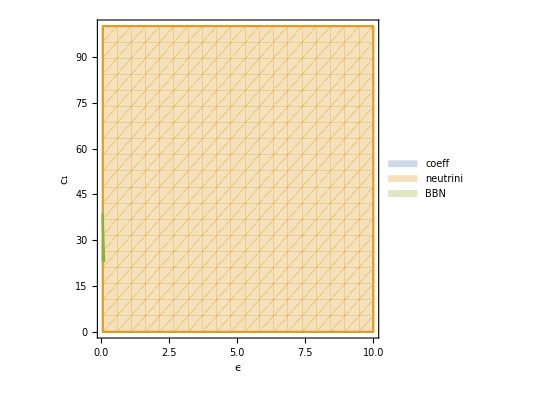

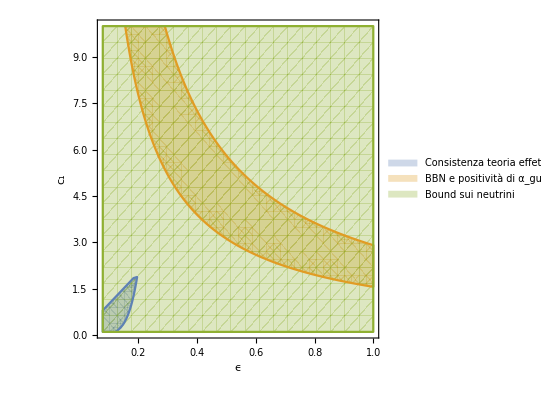

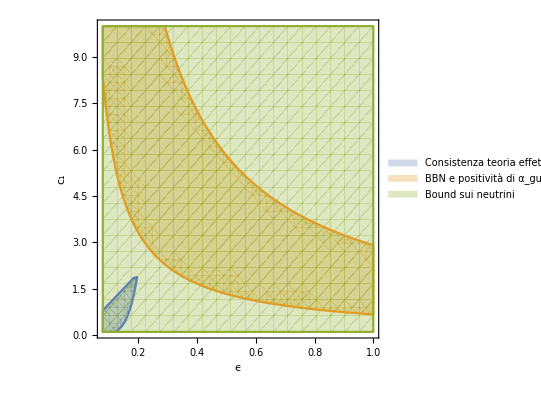

ImplicitRegion::bcond: Null should be a Boolean combination of equations, inequalities, and Element statements.

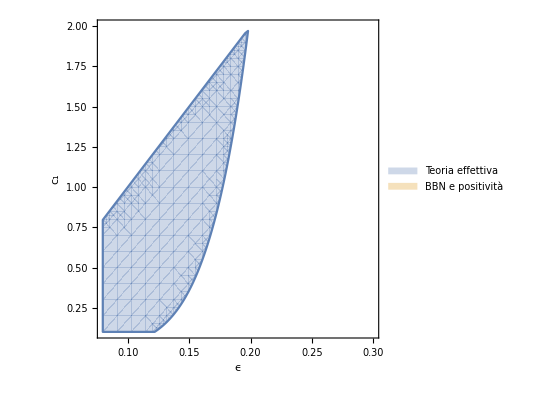

```mathematica
Λgut=5 10^16;
RegionPlot[{0.1<(588 ) ϵ^(1.72)/Subscript[c, 1]^(0.28)<10 && 0.1< Subscript[c, 1]/ϵ<10  , ϵ< Λgut/(10^(14))Subscript[c, 1] , Subscript[c, 1] ϵ < 1.2 (10^(7.59)/Λgut^(0.43)) && Subscript[c, 1] ϵ>(Λgut^(1/9.21)/35.37)},{ϵ,1/(4Pi),10},{Subscript[c, 1],0.1,100}, FrameLabel->{ϵ,Subscript[c, 1]},PlotLegends->{"coeff","neutrini","BBN","Positività"}] (*Condizione su c_5, c_2, neutrini, BBN, *)

RegionPlot[{0.1<3 (1.7 10^(-3)) Subscript[c, 1]^(0.28)/ϵ^(1.72) && 0.1< Subscript[c, 1]/ϵ<10 , (1.4 10^9)/(Λgut^1.8749999999999998 (Subscript[c, 1] ϵ)^4.35)>6.6 10^(-25) && Λgut < Exp[1.54]1.8 10^(14) (Subscript[c, 1] ϵ)^(9.21), ϵ< (Λgut)/(10^(14))Subscript[c, 1]},{ϵ,1/(4Pi),1},{Subscript[c, 1],0.1,10}, FrameLabel->{ϵ,Subscript[c, 1]},PlotLegends->{"Consistenza teoria effettiva","BBN e positività di α_gut","Bound sui neutrini"}] (*Condizione su c_5, c_2, neutrini, BBN, *)
RegionPlot[{0.1<3 (1.7 10^(-3)) Subscript[c, 1]^(0.28)/ϵ^(1.72) && 0.1< Subscript[c, 1]/ϵ<10 , (1.4 10^9)/(Λgut^1.8749999999999998 (Subscript[c, 1] ϵ)^4.35)>6.6 10^(-25) && Λgut < 7.309929002947738 10^18  ϵ^(12.1863799283153895203213323839008808136`15.954589770191005) Subscript[c, 1]^(12.1863799283153895203213323839008808136`15.954589770191005) ,ϵ< (Λgut)/(10^(14))Subscript[c, 1]},{ϵ,1/(4Pi),1},{Subscript[c, 1],0.1,10}, FrameLabel->{ϵ,Subscript[c, 1]},PlotLegends->{"Consistenza teoria effettiva","BBN e positività di α_gut","Bound sui neutrini"}] (*Condizione su c_5, c_2, neutrini, BBN, *)

RegionPlot[{0.1<3 (1.7 10^(-3)) Subscript[c, 1]^(0.28)/ϵ^(1.72)<10 && 0.1< Subscript[c, 1]/ϵ<10 ,},{ϵ,1/(4Pi),0.3},{Subscript[c, 1],0.1,2}, FrameLabel->{ϵ,Subscript[c, 1]},PlotLegends->{"Teoria effettiva","BBN e positività"}] (*Condizione su c_5, c_2, neutrini, BBN, *)
```

## Plot tenendo conto anche di c_3

```mathematica
RegionPlot3D[0.1<3 (1.7 10^(-3)) Subscript[c, 1]^(0.28)/ϵ^(1.72)<10  && 0.1< Subscript[c, 1]/ϵ<10  &&(Subscript[c, 1] ϵ)^(4.35)< 2 ((10^(28))/Λgut^(1.875)) && 1.8  10^(14) Exp[1.54  ϵ (Subscript[c, 3]/Subscript[c, 1])](Subscript[c, 1] ϵ)^(9.21)>Λgut &&ϵ Subscript[c, 3]<Subscript[c, 1],{ϵ,1/(4Pi),0.2},{Subscript[c, 1],0.1,1},{Subscript[c, 3],1,10},AxesLabel->{ϵ,Subscript[c, 1],Subscript[c, 3]},PlotPoints->100, Mesh->None](*Bound di QCD*)
```

-Graphics3D-